```mathematica
data = Import["C:\\Users\\Amit\\Dropbox\\Keystroke Timing\\KeystrokeTiming\\test_mat.mat"];
```

```mathematica
mat = data[[1]];
timing = Flatten@data[[2]];
```

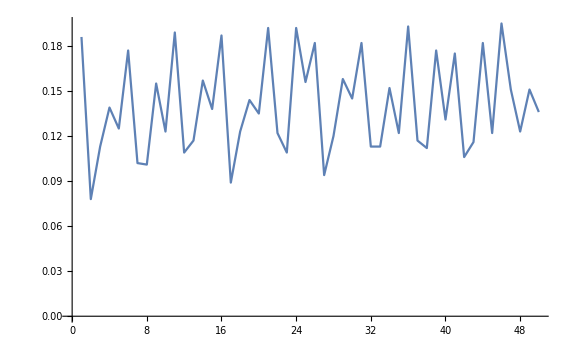

```mathematica
ListLinePlot[timing]
```

```mathematica
mat//MatrixForm
```

(({0}) | ({0}) | ({0}) | ({0.,0.113006,0.101006,0.117007,0.123007,0.109007,0.120007,0.113007,0.112007,0.116007,0.123007}) | ({0}) | ({0}) | ({0})
({0}) | ({0}) | ({0}) | ({0}) | ({0}) | ({0}) | ({0})
({0}) | ({0}) | ({0}) | ({0}) | ({0}) | ({0}) | ({0})
({0}) | ({0}) | ({0}) | ({0}) | ({0.,0.18601,0.177011,0.189011,0.18701,0.192011,0.18201,0.18201,0.193011,0.17501,0.195012}) | ({0}) | ({0.,0.139008,0.155009,0.157009,0.144009,0.192011,0.158009,0.152009,0.17701,0.18201,0.151009})
({0.,0.0780051,0.102005,0.109006,0.089005,0.122007,0.0940051,0.113006,0.117006,0.106006,0.151008}) | ({0}) | ({0}) | ({0}) | ({0}) | ({0}) | ({0})
({0}) | ({0}) | ({0}) | ({0}) | ({0}) | ({0}) | ({0})
({0}) | ({0}) | ({0}) | ({0.,0.125007,0.123007,0.138008,0.135007,0.156009,0.145009,0.122007,0.131007,0.122007,0.136008}) | ({0}) | ({0}) | ({0}))

```mathematica
DE = Flatten@DeleteCases[mat[[4,5]],0.,Infinity]
```

{0.18601,0.177011,0.189011,0.18701,0.192011,0.18201,0.18201,0.193011,0.17501,0.195012}

```mathematica
DeleteCases[mat,0.,Infinity];
```

```mathematica
AD = Flatten@DeleteCases[mat[[1,4]],0.,Infinity]
```

{0.113006,0.101006,0.117007,0.123007,0.109007,0.120007,0.113007,0.112007,0.116007,0.123007}

```mathematica
dehist = HistogramList[DE,{0,.8,.01}]
```

{{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,5,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
dehist1 = Table[{(dehist[[1]][[x]] + dehist[[1]][[x+1]])/2,dehist[[2]][[x]]},{x,1,Length[dehist[[2]]]}];
```

```mathematica
dehist1
```

{{0.005,0},{0.015,0},{0.025,0},{0.035,0},{0.045,0},{0.055,0},{0.065,0},{0.075,0},{0.085,0},{0.095,0},{0.105,0},{0.115,0},{0.125,0},{0.135,0},{0.145,0},{0.155,0},{0.165,0},{0.175,2},{0.185,5},{0.195,3},{0.205,0},{0.215,0},{0.225,0},{0.235,0},{0.245,0},{0.255,0},{0.265,0},{0.275,0},{0.285,0},{0.295,0},{0.305,0},{0.315,0},{0.325,0},{0.335,0},{0.345,0},{0.355,0},{0.365,0},{0.375,0},{0.385,0},{0.395,0},{0.405,0},{0.415,0},{0.425,0},{0.435,0},{0.445,0},{0.455,0},{0.465,0},{0.475,0},{0.485,0},{0.495,0},{0.505,0},{0.515,0},{0.525,0},{0.535,0},{0.545,0},{0.555,0},{0.565,0},{0.575,0},{0.585,0},{0.595,0},{0.605,0},{0.615,0},{0.625,0},{0.635,0},{0.645,0},{0.655,0},{0.665,0},{0.675,0},{0.685,0},{0.695,0},{0.705,0},{0.715,0},{0.725,0},{0.735,0},{0.745,0},{0.755,0},{0.765,0},{0.775,0},{0.785,0},{0.795,0}}

```mathematica
fit = FindFit[dehist1,A Exp[(-(x-μ)^2)/(2 σ^2)],{μ,σ,A},x]
```

{μ→0.186322,σ→0.00802091,A→5.15215}

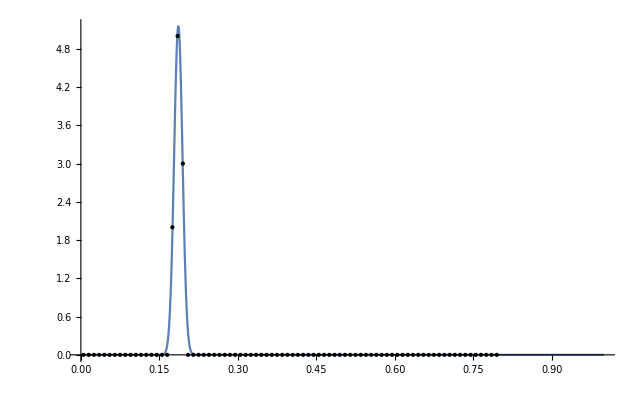

```mathematica
Plot[A Exp[(-(x-μ)^2)/(2 σ^2)]/.fit,{x,0,1},PlotRange->All,Epilog->Map[Point,dehist1]]
```